# 2D Plotting in Mathematica

Christopher Lum
lum@uw.edu

This document accompanies the YouTube video at https://youtu.be/j-utznrXmcY.

## Plot

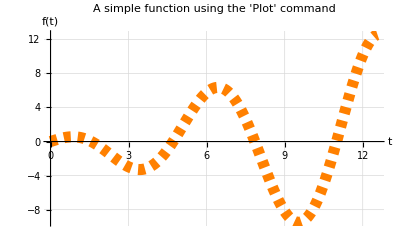

```mathematica
Plot[t*Cos[t],{t,0, 4 π},

(*Plotting options*)
AxesLabel->{"t","f(t)"},
PlotLabel->"A simple function using the 'Plot' command",
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.02]},
PlotRange->All]
```

Adding multiple functions to the same set of axes

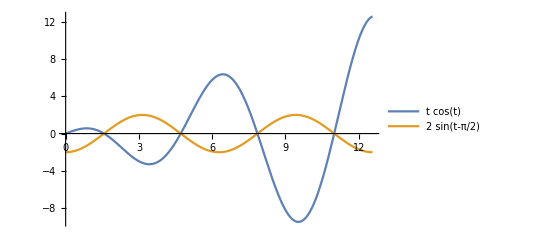

```mathematica
Plot[{t*Cos[t],2 Sin[t-π/2]},{t,0,4 π},

(*Plot options*)
PlotRange->All,
PlotLegends->"Expressions"]
```

Disadvantages
1.  The domain of the functions must be the same.
2.  Difficult to control the plotting style of the two data sets.
3.  Not a lot of legend control

## Show

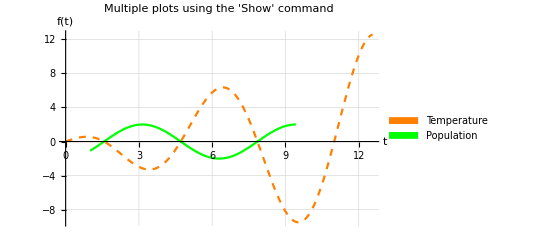

```mathematica
plot1=Plot[t*Cos[t],{t,0,4 π},
PlotStyle->{Orange,Dashed}];

plot2=Plot[2 Sin[t-π/2],{t,1,3 π},
PlotStyle->Green];

Legended[
Show[plot1,plot2,
(*Plot options for the composite graphic*)
PlotLabel->"Multiple plots using the 'Show' command",
AxesLabel->{"t","f(t)"},
PlotRange->All,
GridLines->Automatic],

(*Add legend information*)
SwatchLegend[{Orange,Green},{"Temperature","Population"}]
]
```

## ListPlot

(1 | 2)

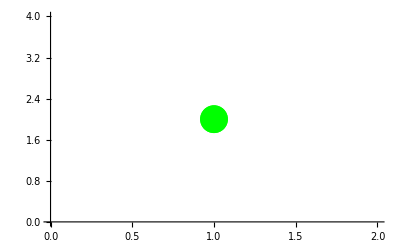

```mathematica
pt1={{1,2}};
pt1//MatrixForm

ListPlot[pt1,
(*plotting options*)
PlotStyle->{Green,PointSize[0.05]}]
```

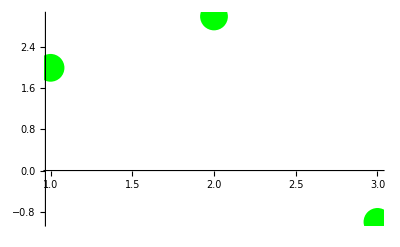

```mathematica
points=({{1, 2}, {2, 3}, {3, -1}});
plotA=ListPlot[points,
PlotStyle->{Green,PointSize[0.05]}]
```

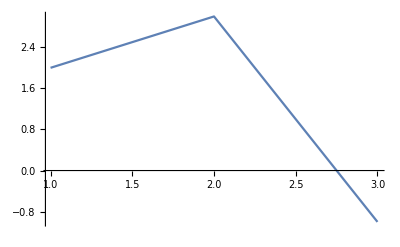

```mathematica
plotB=ListLinePlot[points]
```

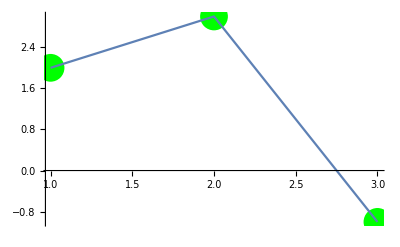

```mathematica
Show[plotA,plotB]
```

Make some fake data

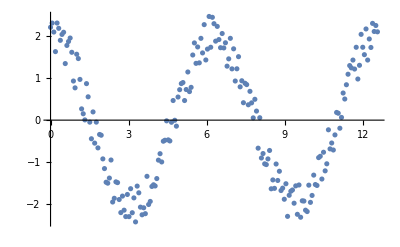

```mathematica
data=Table[{t,2 Cos[t]+RandomReal[]-0.5},{t,0, 4 π, 2π/100}];

dataPlot=ListPlot[data]
```

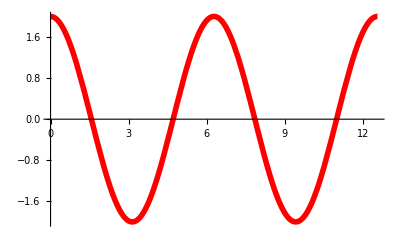

```mathematica
fitPlot=Plot[2 Cos[t],{t,0,4π},
PlotStyle->{Red,Thickness[0.01]}]
```

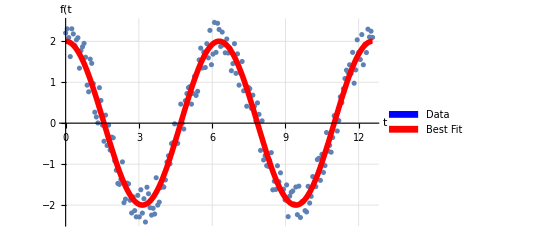

```mathematica
Legended[
Show[dataPlot,fitPlot,
(*Plot Options*)
AxesLabel->{"t","f(t"},
GridLines->Automatic],

(*Add legend information*)
SwatchLegend[{Blue,Red},{"Data","Best Fit"}]
]
```

## DiscretePlot

Plot sin(x) with x every 10 degrees

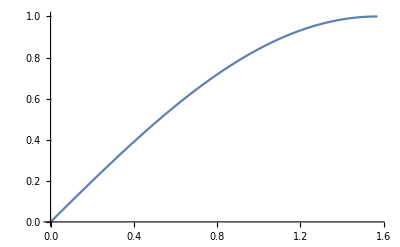

```mathematica
Plot[Sin[x],{x,0,π/2}]
```

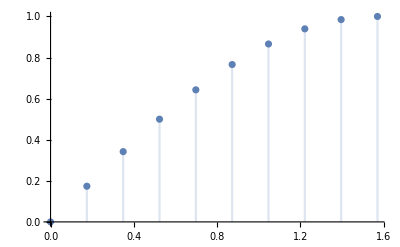

```mathematica
DiscretePlot[Sin[x],{x,0,π/2,10 π/180}]
```

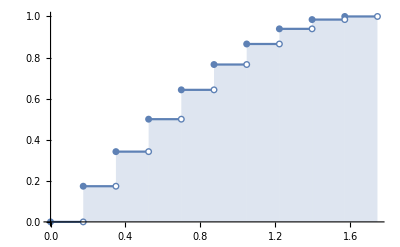

```mathematica
DiscretePlot[Sin[x],{x,0,π/2,10 π/180},
(*additional options*)
ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"}]
```

## Histogram

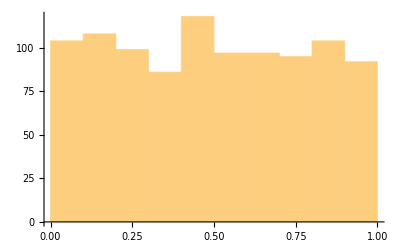

```mathematica
data2=Table[RandomReal[],{i,1,1000}];
data2//MatrixForm;

Histogram[data2]
```

## PieChart

```mathematica
PieChart[{1,2,5}]
```

-Graphics-